```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
l=Flatten @Import["test1.dat"];
nn=Length[l];
```

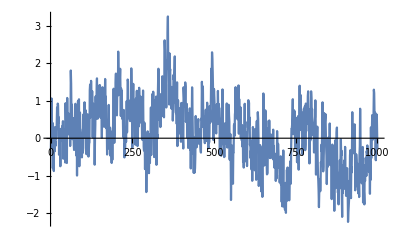

```mathematica
ListLinePlot[Take[l,UpTo[1000]]]
```

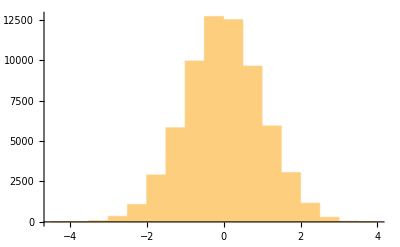

-8.37493×10^-11

1.00001

```mathematica
Histogram[l]
avg=Mean[l]
std=StandardDeviation[l]
```

{{0,1.},{1,0.824317},{2,0.789452},{3,0.751685},{4,0.725512},{5,0.708269},{6,0.69467},{7,0.683483},{8,0.671229},{9,0.662832},{10,0.654314},{11,0.645792},{12,0.638684},{13,0.633233},{14,0.626971},{15,0.621733},{16,0.616122},{17,0.611051},{18,0.606403},{19,0.600779},{20,0.597019},{21,0.5919},{22,0.587549},{23,0.581277},{24,0.577818},{25,0.57577},{26,0.571599},{27,0.568908},{28,0.567542},{29,0.564803},{30,0.563509},{31,0.561123},{32,0.558585},{33,0.555906},{34,0.55443},{35,0.552008},{36,0.549908},{37,0.548555},{38,0.547876},{39,0.545694},{40,0.545387},{41,0.54243},{42,0.541408},{43,0.540086},{44,0.539087},{45,0.536327},{46,0.533608},{47,0.532786},{48,0.530235},{49,0.527392},{50,0.526503},{51,0.525535},{52,0.523435},{53,0.521464},{54,0.520594},{55,0.517721},{56,0.516486},{57,0.515845},{58,0.514692},{59,0.513573},{60,0.511962},{61,0.510998},{62,0.509525},{63,0.508993},{64,0.50729},{65,0.506977},{66,0.50596},{67,0.505156},{68,0.504317},{69,0.502819},{70,0.50273},{71,0.501089},{72,0.498492},{73,0.498043},{74,0.496185},{75,0.494128},{76,0.493641},{77,0.490045},{78,0.490358},{79,0.490461},{80,0.48956},{81,0.489247},{82,0.48821},{83,0.486465},{84,0.486587},{85,0.485609},{86,0.484372},{87,0.482456},{88,0.481572},{89,0.481109},{90,0.480416},{91,0.479971},{92,0.477847},{93,0.475353},{94,0.474474},{95,0.473224},{96,0.471434},{97,0.471845},{98,0.470444},{99,0.469711},{100,0.470414}}

{a→0.833804,b→0.0787046}

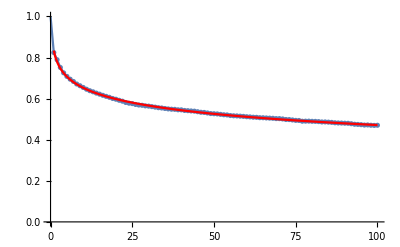

```mathematica
cf=Table[{i,CorrelationFunction[l-avg,i]},{i,0,100}]
p1=ListPlot[cf,PlotRange->{0,1},Joined->True,Mesh->All];
fnc=a-b Log[t];
sol=FindFit[Drop[cf,1],fnc,{a,b},t]
fnc=fnc/.sol;
p2=Plot[fnc,{t,1,100},PlotStyle->Red];
Show[p1,p2]
(* Logarithmic autocorrelation, see Kechner 1982 *)
```

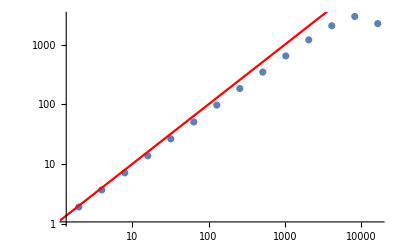

```mathematica
tab=Table[{2^i,StandardDeviation[Map[Total,Partition[l,2^i]]]},{i,14}];
p1=ListLogLogPlot[tab];
p2=LogLogPlot[{1x^(1)},{x,1,Length[l]},PlotStyle->{Red}];
Show[p1,p2]
```

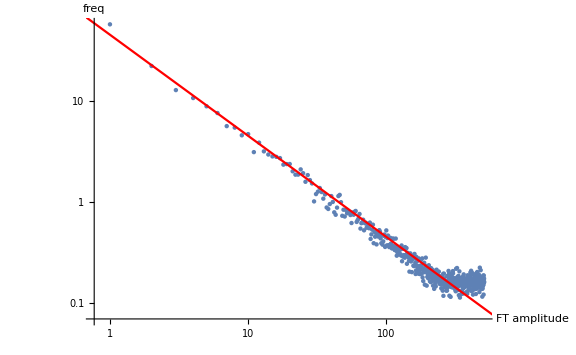

```mathematica
sz=1024;
pl=Partition[l,sz];
(* power spectrum ! *)
pl=Map[(μ=Mean[#];Rest[Take[Abs[Fourier[#-μ]]^2,sz/2]])&,pl];
plavg=Mean[pl];
pft1=ListLogLogPlot[plavg,PlotRange->All,AxesLabel->{"FT amplitude","freq"},LabelStyle->Larger];
pft2=LogLogPlot[{45/ω},{ω,0.1,10^6},PlotStyle->{Red}];
Show[pft1,pft2,ImageSize->8 72]
```